```mathematica
(* Detecting nonlocality in spin-nematic squeezed states as prepared in a spin-1 BEC *)
Needs["SUN`"]; (* https://github.com/kercl/sun *)
Needs["MaTeX`"]
texStyle={FontFamily->"Latin Modern Roman",FontSize->15};
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

```mathematica
Np=30; (* number of parties *)
```

```mathematica
(* Building the totally symmetric irrep *)
MatSU3=LieAlgebraBasisMatrices[Irrep[Np,0]][[1]];
dim=Dimensions[MatSU3][[2]];
MatGM=LieAlgebraBasisMatrices[Irrep[1,0]][[1]];
MatSpin=Normal[LieAlgebraBasisMatrices[Irrep[2]][[1]]];
Ir[A_]:=Sum[2*Tr[A.MatGM[[a]]]*MatSU3[[a]],{a,1,8}]+Np*Tr[A]*IdentityMatrix[dim, SparseArray]/3;
```

```mathematica
(* Spin-mixing Hamiltonian of a spin-1 BEC *)
c2 = -1;  
q = 0.2;
q/c2
J2 = N[Ir[MatSpin[[1]]].Ir[MatSpin[[1]]] + Ir[MatSpin[[2]]].Ir[MatSpin[[2]]]+Ir[MatSpin[[3]]]. Ir[MatSpin[[3]]]];
N0= N[Ir[IdentityMatrix[3]- MatSpin[[3]]. MatSpin[[3]]]];
H =(c2/(2*Np))*J2   -q*N0;
```

-0.2

```mathematica
(* Evolution from polar state |0, N, 0> *)
polar = {Eigenvectors[N0][[1]]};
TauSpace = N@Subdivide[0, 4, 200];
RhoTau = Table[MatrixExp[-I*TauSpace[[t]]*H].polar†.polar.MatrixExp[+I*TauSpace[[t]]*H],{t,1,200}];
```

Eigenvectors::arh: Because finding 496 out of the 496 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvectors.

```mathematica
(* Spin-nematic triad *)
jx = MatSpin[[1]]/2;
qyz = (MatSpin[[2]].MatSpin[[3]]+MatSpin[[3]].MatSpin[[2]])/2;
qp = (MatSpin[[3]].MatSpin[[3]] - MatSpin[[2]].MatSpin[[2]])/2;
Jx = Ir[jx];
Qyz = Ir[qyz];
Qp = Ir[qp];
jx// MatrixForm
qyz// MatrixForm
qp// MatrixForm
```

(0 | 1/(2 √2) | 0
1/(2 √2) | 0 | 1/(2 √2)
0 | 1/(2 √2) | 0)

(0 | -ⅈ/(2 √2) | 0
ⅈ/(2 √2) | 0 | ⅈ/(2 √2)
0 | -ⅈ/(2 √2) | 0)

(1/4 | 0 | 1/4
0 | -1/2 | 0
1/4 | 0 | 1/4)

```mathematica
Cor[rho_]:= {{Tr[Jx.Jx.rho], Re[Tr[Jx.Qyz.rho]]},{Re[Tr[Jx.Qyz.rho]], Tr[Qyz.Qyz.rho]}}
XiMSq[rho_] :=Re[Tr[Qp.rho]^2/Min[Eigenvalues[Cor[rho]]]] /Np                                                           (* Metrological spin-nematic squeezing, >k certifies k+1 entanglement depth  *)
```

```mathematica
res = Table[XiMSq[RhoTau [[t]]], {t,1,200}];
```

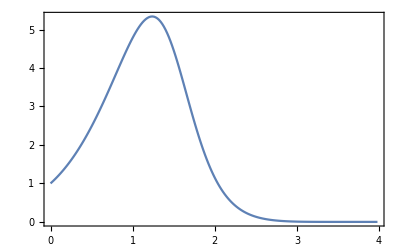

```mathematica
ListLinePlot[Transpose[{TauSpace[[;;200]],res}], Frame->True,BaseStyle->texStyle, FrameLabel->{MaTeX["t", FontSize->17], MaTeX["\mbox{Spin-nematic squeezing }\xi^{-2}", FontSize->17]}]
```

```mathematica
(* Bell operator of family 3 *)
BF3[P00_,P10_,P01_,P11_]:= ((Ir[P00]-Ir[P11]). (Ir[P00]-Ir[P11]) + (Ir[P01]-Ir[P10]). (Ir[P01]-Ir[P10]) + Ir[P00.P11 + P11.P00] + Ir[P01.P10 + P10.P01]);
(* Minimum eigenvalue *)
Projs[m_] := {2*m.m+m, 2*m.m-m, IdentityMatrix[3]-4*m.m};
```

```mathematica
SqzedOp[rho_] := Eigenvectors[Cor[rho]][[2]][[1]]* jx  + Eigenvectors[Cor[rho]][[2]][[2]]*qyz
Data[rho_] := Re[{Tr[Ir[SqzedOp[rho]].Ir[SqzedOp[rho]].rho]/Tr[rho.Ir[qp.qp]],Tr[Qp.rho]/Tr[rho.Ir[qp.qp]]/2, Tr[rho.Ir[qp.qp]]*4/Np }];
OptTh[Data_]:=Re[ArcSin[s/. Minimize[{Re[(1-s^2)*Data[[1]] + s*Data[[2]] +s^2], s^2≤1}, s][[2]]]];
Meas[rho_,th_]:= {Cos[th]*SqzedOp[rho] + Sin[th]*qp, Cos[th]*SqzedOp[rho]  - Sin[th]*qp};
Wit[rho_,th_] :=  Re[Tr[BF3[Projs[Meas[rho,th][[1]]][[1]],Projs[Meas[rho,th][[1]]][[3]],Projs[Meas[rho,th][[2]]][[3]],Projs[Meas[rho,th][[2]]][[2]]].rho]];
```

```mathematica
resW = Table[Wit[RhoTau[[t]], OptTh[Data[RhoTau[[t]]]]],{t,1,200}];
```

```mathematica
DatTau = Table[Data[RhoTau[[t]]], {t,1,200}];
```

```mathematica
W[Data_]:=Np*Minimize[{Re[(1-s^2)*Data[[1]] + s*Data[[2]] +s^2 + 2*(1-Data[[3]])/Data[[3]]], s^2≤1}, s];
```

```mathematica
resB = Table[W[DatTau[[t]]][[1]],{t,1,200} ];
```

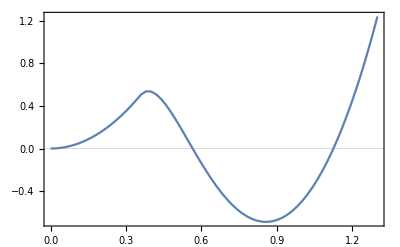

```mathematica
Show[ListLinePlot[Transpose[{TauSpace[[1;;66]],resB[[1;;66]]}], FrameLabel->{MaTeX["t", FontSize->18],MaTeX["\mbox{Bell violation }<\hat{\mathcal{B}}>", FontSize->18]}, Frame->True,GridLines->{None,{0}}],BaseStyle->{FontSize->15}]
```

```mathematica
(* Of course, won't violate the QUBIT bound *)
```

```mathematica
(* Witness *)
Minimize[{(1-s^2)*x+s*y+s^2+2*zt-b/z, s^2≤1,1/Np≤x/y^2, 0≤y≤1 },{s}]
```

{Piecewise[{{(-b+z-y z+2 z zt)/z, (0<y≤1&&x==1&&z>0)||(0<y≤1&&x==1&&z<0)||(0<y≤1&&x>1&&z>0)||(0<y≤1&&x>1&&z<0)||(0<y≤1&&(2-y)/2<x<1&&z>0)||(0<y≤1&&(2-y)/2<x<1&&z<0)}, {(4 b-4 b x-4 x z+4 x^2 z+y^2 z-8 z zt+8 x z zt)/(4 (-1+x) z), (0<y≤1&&y^2/30≤x≤(2-y)/2&&z>0)||(0<y≤1&&y^2/30≤x≤(2-y)/2&&z<0)}, {∞, True}}],{s→Piecewise[{{-1, (0<y≤1&&x==1&&z>0)||(0<y≤1&&x==1&&z<0)}, {y/(2 (-1+x)), (0<y≤1&&y^2/30≤x≤(2-y)/2&&z>0)||(0<y≤1&&y^2/30≤x≤(2-y)/2&&z<0)}, {(y+√((-2+2 x+y)^2/(-1+x)^2)-x √((-2+2 x+y)^2/(-1+x)^2))/(2 (-1+x)), (0<y≤1&&x>1&&z>0)||(0<y≤1&&x>1&&z<0)}, {(y-√((-2+2 x+y)^2/(-1+x)^2)+x √((-2+2 x+y)^2/(-1+x)^2))/(2 (-1+x)), (0<y≤1&&(2-y)/2<x<1&&z>0)||(0<y≤1&&(2-y)/2<x<1&&z<0)}, {Indeterminate, True}}]}}

```mathematica
Solve[(4 b-4 b x-4 x z+4 x^2 z+y^2 z-8 z zt+8 x z zt)/(4 (-1+x) z)==0 ,x]
```

{{x→(4 b+4 z-8 z zt-√(-16 z (4 b+y^2 z-8 z zt)+(-4 b-4 z+8 z zt)^2))/(8 z)},{x→(4 b+4 z-8 z zt+√(-16 z (4 b+y^2 z-8 z zt)+(-4 b-4 z+8 z zt)^2))/(8 z)}}

```mathematica
Simplify[(x -  (4 b+4 z-8 z zt-√(-16 z (4 b+y^2 z-8 z zt)+(-4 b-4 z+8 z zt)^2))/(8 z) /. zt ->(1-z)/z)≥0]
```

(2-b-3 z+2 x z+√(4+b^2+2 b (-2+z)-4 z+z^2-y^2 z^2))/z≥0

```mathematica
(* x = <Jx^2>/(N-N0), y = |<Jy>|/(N-N0), z = (N-N0)/N (Spect(J) = [-1, 0, 1]). Metrological spin-nematic squeezing criterion x/y^2 <= kz *)
```

```mathematica
DatTau = Import["DatTau.dat"];
Show[
 ContourPlot3D[y^2/x ==z^{-1}, {x,0,1}, {y,0,1}, {z,0,1}, ContourStyle->Directive[Green,Opacity[0.8],Specularity[White,30]], Mesh->None], ContourPlot3D[2 x+√(-y^2+(-2+z)^2/z^2)+2/z==3, {x,0,1}, {y,0,1}, {z,0,1},ContourStyle->Directive[Orange,Opacity[0.8],Specularity[White,30]], Mesh->None] ,
Graphics3D[{Thick,Blue,Line[Abs[DatTau[[1;;113]]]]}],
AxesLabel->{MaTeX["x", FontSize->18],MaTeX["y", FontSize->18],MaTeX["z", FontSize->18]},BaseStyle->texStyle, PlotRange->{{0,1}, {0.55,1}, {0,1}}, BoxRatios->{1,1,0.4}]
```

-Graphics3D-

```mathematica
(*Bogoliubov bound check *)
```

```mathematica
Jx = Ir[MatGM[[1]]];
Jy = Ir[MatGM[[2]]];
Bth[th_]:=4*Cos[th]^2*Jx.Jx +2*Sin[th]*Jy +Sin[th]^2*Np*IdentityMatrix[dim](* m0 = cos + sin, m1 = cos - sin, angle between 0 and 1 is 2theta *)
Thvals = N@Subdivide[0,2*Pi,360];
Bthth =  Table[Min[N[Eigenvalues[Bth[Thvals[[t]]]]]],{t,1,360}];
```

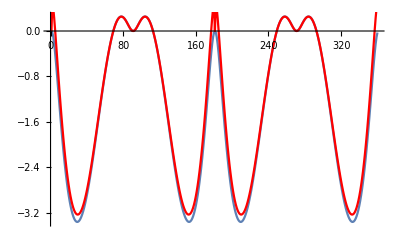

```mathematica
EGs[th_]:=Sin[th]^2*Np-Abs[Sin[th]]*(Np+1)+(1/2)*Sqrt[(2 Abs[Sin[th]] + 4*Cos[th]^2*Np/2)^2 - ( 4*Cos[th]^2*Np/2)^2]
Show[ListLinePlot[Bthth],ListLinePlot[EGsth, PlotStyle->Red]]
```

```mathematica
FullSimplify[Sin[th]^2*Npa-Abs[Sin[th]]*(Npa+1)+(1/2)*Sqrt[(2 Abs[Sin[th]] + 4*Cos[th]^2*Npa/2)^2 - ( 4*Cos[th]^2*Npa/2)^2] /. th -> Pi/6]
```

1/4 (-2-Npa+2 √(1+3 Npa))

```mathematica
N[1/4 (-2-Npa+2 √(1+3 Npa)) /. Npa->Np]
```

-3.2303

```mathematica
Min[Bthth]
```

-3.3643